```mathematica
Clear[dz]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}]
Ds[n_,s_,z_]:=Sum[ j^-s dz[j,z],{j,1,n}]
ddz1[n_, m_,s_,z_] := Sum[a^-s b^-s dz[a,z]dz[b,-z],{a,1,n}, {b,1,m/a^(N@Log[m]/Log[n])}]
ldz[n_,m_,s_]:=D[ ddz1[n,m,s,z],z]/.z->0
sddz[n_, m_,s_,t_,z_] := Sum[a^-s b^-t dz[a,z]dz[b,-z],{a,1,n}, {b,1,(n/a)^(N@Log[m]/Log[n])}]
sldz[n_,m_,s_,t_]:=D[ sddz[n,m,s,t,z],z]/.z->0
pr[n_,s_] := Sum[ FullSimplify[MangoldtLambda[j]/Log[j]] j^-s,{j,2,n}]
ch[n_] := -Sum[MangoldtLambda[j],{j,2,n}]
```

```mathematica
ldz[1200,320,-3]
```

13317518631487/180

```mathematica
pr[1200,-3]-pr[320,-3]
```

13317518631487/180

```mathematica
sldz[1200,320,-2,-4]
```

-159395771066767/1260

```mathematica
pr[1200,-2]-pr[320,-4]
```

-159395771066767/1260

```mathematica
fo[n_,s_,k_]:=fo[n,s,k]=Sum[ Abs[MoebiusMu[j]] j^-s fo[Floor[n/j],s,k-1],{j,2,n}]
fo[n_,s_,0]:=UnitStep[n-1]
lf[n_,s_]:=Sum[ (-1)^(k+1)/k fo[n,s,k],{k,1,Log2@n}]
```

```mathematica
lf[1000,-2]
```

15167671034/315

```mathematica
pr[1000,-2] - pr[1000^(1/2),-4]
```

15167671034/315

```mathematica
N[D[ldz[1000,910,s],s]/.s->0]
```

-92.6396

```mathematica
N[ch[1000]-ch[910]]
```

-92.6396

```mathematica
Expand[ddz1[100,50,1,z]]
```

1+(5709300759326076208729 z)/38875468949180319102336+(4601729822212889 z^2)/190035075607977600-(598781923 z^3)/33418344960+(6331 z^4)/422400+(397 z^5)/69120-z^6/7680

```mathematica
Expand[ddz1[100,50,1,z]]
```

1+(5709300759326076208729 z)/38875468949180319102336+(4601729822212889 z^2)/190035075607977600-(598781923 z^3)/33418344960+(6331 z^4)/422400+(397 z^5)/69120-z^6/7680

```mathematica
D[ddz1[100,50,1,z],z]/.z->0
```

5709300759326076208729/38875468949180319102336

```mathematica
pr[100,1]-pr[50,1]
```

5709300759326076208729/38875468949180319102336

```mathematica
N[D[D[ddz1[100,50,s,z],z]/.z->0,s]/.s->0]
```

-44.5599

```mathematica
N[ch[100]-ch[50]]
```

-44.5599

```mathematica
Expand@(Ds[100,-1,z]-Ds[50,-1,z])
```

(9155 z)/12+(129325 z^2)/72+(11261 z^3)/12+(18571 z^4)/72+(56 z^5)/3+(8 z^6)/9

```mathematica
Expand@ddz1[100,50,-1,z]
```

1+(9155 z)/12+(223717 z^2)/360-(43 z^3)/12+(4223 z^4)/72+(92 z^5)/3-(4 z^6)/45

```mathematica
aa[n_,m_]:=Sum[ MoebiusMu[k],{j,1,n},{k,1,m/(j^(N@Log[m]/Log[n]))}]
```

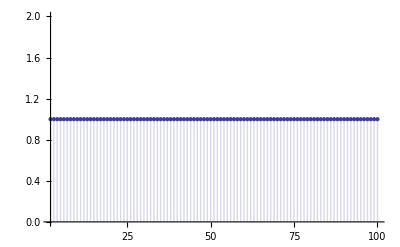

```mathematica
DiscretePlot[aa[n,n],{n,2,100}]
```

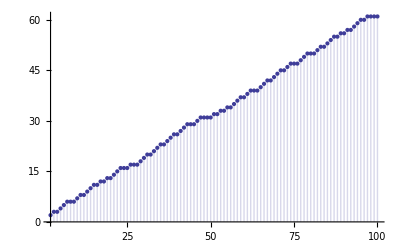

```mathematica
DiscretePlot[ddz1b[n,n^(1/2)],{n,2,100}]
```

```mathematica
ddz1[n_, m_,s_,z_] := Sum[a^-s b^-s dz[a,z]dz[b,-z],{a,1,n}, {b,1,m/a^(N@Log[m]/Log[n])}]
ddz1a[n_, m_] := Sum[ dz[a,1]dz[b,-1],{a,1,n}, {b,1,m/a^(N@Log[m]/Log[n])}]
ddz1b[n_, m_] := Sum[ dz[a,1]dz[b,-1],{a,1,n}, {b,1,m/a^(N@Log[m]/Log[n])}]
```

```mathematica
FullSimplify@D[D[(Zeta[2s]/Zeta[s])^z,z]/.z->0,s]
```

-Zeta'[s]/Zeta[s]+(2 Zeta'[2 s])/Zeta[2 s]

```mathematica
ri[]:=RandomInteger[{10,100}];rr[]:=RandomReal[{-4,4}]+RandomReal[{-4,4}]I
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_]:=Sum[ dz[j,z],{j,1,n}]
zeta[n_,s_,z_,k_]:=1+((z+1)/k-1) Sum[j^-s zeta[n/j,s,z,k+1],{j,2,n}]
F[n_,i_,k_,z_]:=If[Prime[i]>n,1,(1+(z-1)/k)F[n/Prime[i],i,k+1,z]+F[n,i+1,1,z]]
Grid[Table[Chop[Dz[a=143,s+t I]-F[a,1,1,s+t I]],{s,-1.5,4,.7},{t,-1.1,4,.7}]]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Limit[ (1-(x+1)^(1-s))Sum[ j^-s,{j,1,Floor[x]}],x->Infinity]
```

Limit[(1-(1+x)^(1-s)) HarmonicNumber[Floor[x],s],x→∞]

```mathematica
Grid[Table[(FullSimplify[dz[n,z]dz[m,-z]]/z)/.z->0,{n,1,20},{m,1,10/n^Log[20,10]}]]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity | -1 | -1 | -1/2 | -1 | 0 | -1 | -1/3 | -1/2 | 0
1 | 0 | 0 | 0 | 0 |  |  |  |  | 
1 | 0 | 0 | 0 |  |  |  |  |  | 
1/2 | 0 | 0 |  |  |  |  |  |  | 
1 | 0 |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  | 
1 | 0 |  |  |  |  |  |  |  | 
1/3 | 0 |  |  |  |  |  |  |  | 
1/2 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  | 
1/4 |  |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |

```mathematica
Grid[Table[D[D[Expand[n^-s dz[n,z]m^-s dz[m,-z]],s]/.s->0,z]/.z->0,{n,1,30},{m,1,10}]]
```

0 | Log[2] | Log[3] | Log[2] | Log[5] | 0 | Log[7] | Log[2] | Log[9]/2 | 0
-Log[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[7] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[9]/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[11] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[17] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[19] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[23] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[25]/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[29] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Grid[Table[D[Expand[n^-s dz[n,z]m^-s dz[m,-z]],z]/.z->0,{n,1,30},{m,1,10}]]
```

0 | -2^-s | -3^-s | -2^(-1-2 s) | -5^-s | 0 | -7^-s | -1/3 2^(-3 s) | -9^-s/2 | 0
2^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2^(-1-2 s) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2^(-3 s)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9^-s/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2^(-2-4 s) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25^-s/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3^(-1-3 s) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29^-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Grid[Table[Expand[dz[n,z]dz[m,-z]],{n,1,30},{m,1,10}]]
```

1 | -z | -z | -z/2+z^2/2 | -z | z^2 | -z | -z/3+z^2/2-z^3/6 | -z/2+z^2/2 | z^2
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z/2+z^2/2 | -z^2/2-z^3/2 | -z^2/2-z^3/2 | -z^2/4+z^4/4 | -z^2/2-z^3/2 | z^3/2+z^4/2 | -z^2/2-z^3/2 | -z^2/6+z^3/12+z^4/6-z^5/12 | -z^2/4+z^4/4 | z^3/2+z^4/2
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z^2 | -z^3 | -z^3 | -z^3/2+z^4/2 | -z^3 | z^4 | -z^3 | -z^3/3+z^4/2-z^5/6 | -z^3/2+z^4/2 | z^4
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z/3+z^2/2+z^3/6 | -z^2/3-z^3/2-z^4/6 | -z^2/3-z^3/2-z^4/6 | -z^2/6-z^3/12+z^4/6+z^5/12 | -z^2/3-z^3/2-z^4/6 | z^3/3+z^4/2+z^5/6 | -z^2/3-z^3/2-z^4/6 | -z^2/9+(5 z^4)/36-z^6/36 | -z^2/6-z^3/12+z^4/6+z^5/12 | z^3/3+z^4/2+z^5/6
z/2+z^2/2 | -z^2/2-z^3/2 | -z^2/2-z^3/2 | -z^2/4+z^4/4 | -z^2/2-z^3/2 | z^3/2+z^4/2 | -z^2/2-z^3/2 | -z^2/6+z^3/12+z^4/6-z^5/12 | -z^2/4+z^4/4 | z^3/2+z^4/2
z^2 | -z^3 | -z^3 | -z^3/2+z^4/2 | -z^3 | z^4 | -z^3 | -z^3/3+z^4/2-z^5/6 | -z^3/2+z^4/2 | z^4
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z^2/2+z^3/2 | -z^3/2-z^4/2 | -z^3/2-z^4/2 | -z^3/4+z^5/4 | -z^3/2-z^4/2 | z^4/2+z^5/2 | -z^3/2-z^4/2 | -z^3/6+z^4/12+z^5/6-z^6/12 | -z^3/4+z^5/4 | z^4/2+z^5/2
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z^2 | -z^3 | -z^3 | -z^3/2+z^4/2 | -z^3 | z^4 | -z^3 | -z^3/3+z^4/2-z^5/6 | -z^3/2+z^4/2 | z^4
z^2 | -z^3 | -z^3 | -z^3/2+z^4/2 | -z^3 | z^4 | -z^3 | -z^3/3+z^4/2-z^5/6 | -z^3/2+z^4/2 | z^4
z/4+(11 z^2)/24+z^3/4+z^4/24 | -z^2/4-(11 z^3)/24-z^4/4-z^5/24 | -z^2/4-(11 z^3)/24-z^4/4-z^5/24 | -z^2/8-(5 z^3)/48+(5 z^4)/48+(5 z^5)/48+z^6/48 | -z^2/4-(11 z^3)/24-z^4/4-z^5/24 | z^3/4+(11 z^4)/24+z^5/4+z^6/24 | -z^2/4-(11 z^3)/24-z^4/4-z^5/24 | -z^2/12-z^3/36+(5 z^4)/48+(5 z^5)/144-z^6/48-z^7/144 | -z^2/8-(5 z^3)/48+(5 z^4)/48+(5 z^5)/48+z^6/48 | z^3/4+(11 z^4)/24+z^5/4+z^6/24
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z^2/2+z^3/2 | -z^3/2-z^4/2 | -z^3/2-z^4/2 | -z^3/4+z^5/4 | -z^3/2-z^4/2 | z^4/2+z^5/2 | -z^3/2-z^4/2 | -z^3/6+z^4/12+z^5/6-z^6/12 | -z^3/4+z^5/4 | z^4/2+z^5/2
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z^2/2+z^3/2 | -z^3/2-z^4/2 | -z^3/2-z^4/2 | -z^3/4+z^5/4 | -z^3/2-z^4/2 | z^4/2+z^5/2 | -z^3/2-z^4/2 | -z^3/6+z^4/12+z^5/6-z^6/12 | -z^3/4+z^5/4 | z^4/2+z^5/2
z^2 | -z^3 | -z^3 | -z^3/2+z^4/2 | -z^3 | z^4 | -z^3 | -z^3/3+z^4/2-z^5/6 | -z^3/2+z^4/2 | z^4
z^2 | -z^3 | -z^3 | -z^3/2+z^4/2 | -z^3 | z^4 | -z^3 | -z^3/3+z^4/2-z^5/6 | -z^3/2+z^4/2 | z^4
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z^2/3+z^3/2+z^4/6 | -z^3/3-z^4/2-z^5/6 | -z^3/3-z^4/2-z^5/6 | -z^3/6-z^4/12+z^5/6+z^6/12 | -z^3/3-z^4/2-z^5/6 | z^4/3+z^5/2+z^6/6 | -z^3/3-z^4/2-z^5/6 | -z^3/9+(5 z^5)/36-z^7/36 | -z^3/6-z^4/12+z^5/6+z^6/12 | z^4/3+z^5/2+z^6/6
z/2+z^2/2 | -z^2/2-z^3/2 | -z^2/2-z^3/2 | -z^2/4+z^4/4 | -z^2/2-z^3/2 | z^3/2+z^4/2 | -z^2/2-z^3/2 | -z^2/6+z^3/12+z^4/6-z^5/12 | -z^2/4+z^4/4 | z^3/2+z^4/2
z^2 | -z^3 | -z^3 | -z^3/2+z^4/2 | -z^3 | z^4 | -z^3 | -z^3/3+z^4/2-z^5/6 | -z^3/2+z^4/2 | z^4
z/3+z^2/2+z^3/6 | -z^2/3-z^3/2-z^4/6 | -z^2/3-z^3/2-z^4/6 | -z^2/6-z^3/12+z^4/6+z^5/12 | -z^2/3-z^3/2-z^4/6 | z^3/3+z^4/2+z^5/6 | -z^2/3-z^3/2-z^4/6 | -z^2/9+(5 z^4)/36-z^6/36 | -z^2/6-z^3/12+z^4/6+z^5/12 | z^3/3+z^4/2+z^5/6
z^2/2+z^3/2 | -z^3/2-z^4/2 | -z^3/2-z^4/2 | -z^3/4+z^5/4 | -z^3/2-z^4/2 | z^4/2+z^5/2 | -z^3/2-z^4/2 | -z^3/6+z^4/12+z^5/6-z^6/12 | -z^3/4+z^5/4 | z^4/2+z^5/2
z | -z^2 | -z^2 | -z^2/2+z^3/2 | -z^2 | z^3 | -z^2 | -z^2/3+z^3/2-z^4/6 | -z^2/2+z^3/2 | z^3
z^3 | -z^4 | -z^4 | -z^4/2+z^5/2 | -z^4 | z^5 | -z^4 | -z^4/3+z^5/2-z^6/6 | -z^4/2+z^5/2 | z^5

```mathematica
D[Expand[Dz[30,z]Dz[10,-z]],z]/.z->0
```

85/12

```mathematica
(D[Expand[Dz[30,z]],z]/.z->0)-(D[Expand[Dz[10,z]],z]/.z->0)
```

85/12